# ODE simulation RESEAU BOOLEEN VERLINGUE 2016 -- NORMAL VARIANT

```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
<< BooleanToLogisticODE`
```

```mathematica
Unprotect[t]; Clear[t]; Protect[t];
```

## RESEAU BOOLEEN VERLINGUE 2016 -- NORMAL VARIANT

```mathematica
FBraw = {
 Insulin -> True,
 GF -> True,
 Therapy -> True,
 Senescence -> (mTORC1 S6K1 || p16) && (p16 || p21),
 G1 S -> CDK2 && E2F1 && Metabolism && !p21,
 MAPK -> GF && !PP2A,
 p16 -> !E2F1 && MAPK && !p53 && !PRC,
 MDM2 -> (AKT || p16 || p53) && !E2F1 && !mTORC1 S6K1 && !MYC,
 p53 -> !MDM2,
 p21 -> !AKT && (FOXO || p53) && !MYC,
 AKT -> (CDK2 || IRS PIK3CA) && !PP2A && !PTEN,
 mTORC1 S6K1 -> !AMPK && !TSC,
 ATP -> Metabolism,
 IRS PIK3CA -> Insulin,
 AMPK -> !ATP && p53,
 PTEN -> !AKT && p53,
 TSC -> !AKT && AMPK && !MAPK,
 MYC -> E2F1 && MAPK && mTORC1 S6K1 && !p53,
 CDK2 -> (E2F1 || MYC) && mTORC1 S6K1 && !p21,
 pRB -> !CDK2,
 E2F1 -> E2F1 && (GF || MYC) && !pRB,
 PRC -> !AKT && MYC,
 Metabolism -> (AKT || PP1C) && (MAPK || mTORC1 S6K1),
 PP2A -> !mTORC1 S6K1,
 FOXO -> !AKT && (AMPK || Metabolism || p16) && !MAPK,
 PP1C -> AKT || MAPK
};
```

```mathematica
FB = DeleteCases[FBraw, Therapy -> _];
```

```mathematica
FBmin = FB /. (lhs_ -> rhs_) :> (lhs -> BooleanMinimize[rhs, "DNF"]);
```

```mathematica
κ = <|
  Insulin -> 86.8963, GF -> 72.4351, Senescence -> 94.6186, G1 S -> 93.7670,
  MAPK -> 62.8255, p16 -> 84.1431, MDM2 -> 96.6196, p53 -> 54.0983, p21 -> 64.8349,
  AKT -> 53.5813, mTORC1 S6K1 -> 74.3393, ATP -> 73.6526,
  IRS PIK3CA -> 64.9635, AMPK -> 57.7498, PTEN -> 60.5431, TSC -> 60.4151,
  MYC -> 58.4264, CDK2 -> 72.6472, pRB -> 85.5416, E2F1 -> 54.0984, PRC -> 81.4405,
  Metabolism -> 62.1464, PP2A -> 80.4183, FOXO -> 93.0308, PP1C -> 88.6539
|>;

γ = <|
  Insulin -> 0.3092, GF -> 1.2442, Senescence -> 0.5957, G1 S -> 0.8056,
  MAPK -> 1.3449, p16 -> 0.3772, MDM2 -> 1.5876, p53 -> 0.4196, p21 -> 1.1774,
  AKT -> 0.3051, mTORC1 S6K1 -> 1.2706, ATP -> 1.7608,
  IRS PIK3CA -> 0.8646, AMPK -> 1.4242, PTEN -> 0.8750, TSC -> 0.9335,
  MYC -> 1.1724, CDK2 -> 0.6951, pRB -> 1.4941, E2F1 -> 0.8848, PRC -> 1.5997,
  Metabolism -> 0.5707, PP2A -> 0.7755, FOXO -> 0.3583, PP1C -> 1.5265
|>;

θ = <|
  Insulin -> 15.6650, GF -> 15.8662, Senescence -> 17.3886, G1 S -> 18.2190,
  MAPK -> 16.8623, p16 -> 15.4681, MDM2 -> 12.5930, p53 -> 15.5627, p21 -> 15.2005,
  AKT -> 10.5953, mTORC1 S6K1 -> 10.6927, ATP -> 15.8599,
  IRS PIK3CA -> 12.8231, AMPK -> 15.7422, PTEN -> 19.4743, TSC -> 18.9398,
  MYC -> 13.5479, CDK2 -> 16.2350, pRB -> 13.7492, E2F1 -> 18.3530, PRC -> 16.2775,
  Metabolism -> 18.2466, PP2A -> 19.7952, FOXO -> 13.8287, PP1C -> 11.1833
|>;

n = 4;

initialcondition = <|
  Insulin -> 63.5812, GF -> 14.7108, Senescence -> 61.7234, G1 S -> 96.8135,
  MAPK -> 95.4912, p16 -> 10.3455, MDM2 -> 9.5610, p53 -> 62.8235, p21 -> 51.1062,
  AKT -> 35.3197, mTORC1 S6K1 -> 28.5190, ATP -> 46.3278,
  IRS PIK3CA -> 94.5954, AMPK -> 15.4485, PTEN -> 95.8189, TSC -> 84.1208,
  MYC -> 69.4285, CDK2 -> 76.1456, pRB -> 17.0991, E2F1 -> 55.7069, PRC -> 77.6568,
  Metabolism -> 20.7439, PP2A -> 56.7135, FOXO -> 0.8879, PP1C -> 41.6233
|>;
```

#### ODE

```mathematica
system1 = BooleanToOdeSystem[FBmin, t, κ, γ, θ, n,
   initialcondition, {logisticm, logisticp}];
```

```mathematica
fun = (#[t] &) /@ Keys[FB];
```

```mathematica
S = NDSolve[system1, Keys[FB], {t, 0, 60}, MaxSteps -> Infinity];
```

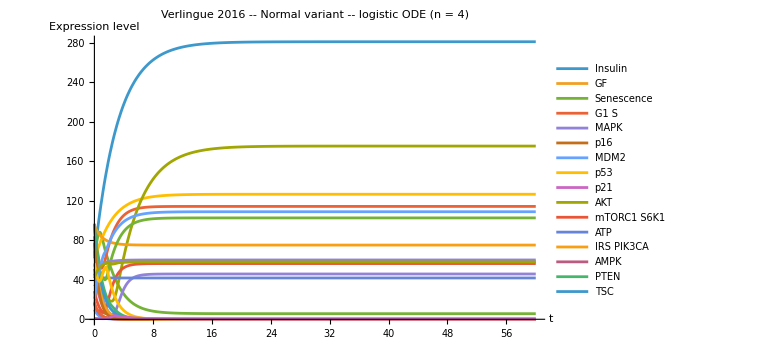

```mathematica
Plot[Evaluate[fun /. S[[1]]], {t, 0, 60}, PlotRange -> All,
 PlotLegends -> Keys[FB], ImageSize -> Large,
 AxesLabel -> {"t", "Expression level"},
 PlotLabel -> "Verlingue 2016 -- Normal variant -- logistic ODE (n = 4)"]
```

#### Stable states (check)

```mathematica
stateAktActiveNonCycling = <|Insulin -> True, GF -> True, Senescence -> False,
   G1 S -> False, MAPK -> True, p16 -> False, MDM2 -> False,
   p53 -> True, p21 -> False, AKT -> True, mTORC1 S6K1 -> True,
   ATP -> True, IRS PIK3CA -> True, AMPK -> False, PTEN -> False,
   TSC -> False, MYC -> False, CDK2 -> False, pRB -> True, E2F1 -> False,
   PRC -> False, Metabolism -> True, PP2A -> False, FOXO -> False, PP1C -> True|>;

stateSenescent = <|Insulin -> True, GF -> True, Senescence -> True,
   G1 S -> False, MAPK -> True, p16 -> False, MDM2 -> False,
   p53 -> True, p21 -> True, AKT -> False, mTORC1 S6K1 -> True,
   ATP -> True, IRS PIK3CA -> True, AMPK -> False, PTEN -> True,
   TSC -> False, MYC -> False, CDK2 -> False, pRB -> True, E2F1 -> False,
   PRC -> False, Metabolism -> True, PP2A -> False, FOXO -> False, PP1C -> True|>;

stateProliferative = <|Insulin -> True, GF -> True, Senescence -> False,
   G1 S -> True, MAPK -> True, p16 -> False, MDM2 -> False,
   p53 -> True, p21 -> False, AKT -> True, mTORC1 S6K1 -> True,
   ATP -> True, IRS PIK3CA -> True, AMPK -> False, PTEN -> False,
   TSC -> False, MYC -> False, CDK2 -> True, pRB -> False, E2F1 -> True,
   PRC -> False, Metabolism -> True, PP2A -> False, FOXO -> False, PP1C -> True|>;

checkFixedPoint[state_] := AllTrue[FB, (#[[1]] /. state) === (#[[2]] /. state) &];

{checkFixedPoint[stateAktActiveNonCycling], checkFixedPoint[stateSenescent],
 checkFixedPoint[stateProliferative]}
```

{True,True,True}